```mathematica
(*Define Fundamental Constants*)
c=2.99792*10^8;  (*Speed of light in meters per second*)
Lplanck=1.616255*10^-35; (*Planck length in meters*)
Tplanck = 5.391247*10^-44; (*Planck time in seconds*)

(*Define the Radius of the Observable Universe*)
Rtoday=4.286332662*10^26;
REonReset = 4.274 *10^38;
R=Rtoday;

(*Calculate the Vacuum Energy Density*)
energyDensity=N[Pi*c^2/R];

(*Calculate the Vacuum Mass Density*)
massDensity=N[Pi/R];

(*Calculate current Curvature Factor*)
CurvatureFactor = 1+1/(Pi^2);

(*Compute the Hubble Expansion Rate*)
hubbleRate=N[(c/R)*  Pi ,15];
(*Convert H into km/s/Mpc*)
hubbleRatekmsMpc=N[hubbleRate*(3.086*10^19), 15]; 

(*Compute the Age of the Universe*)
(*Universe age=1/Hubble constant in seconds*)
universeAgeseconds=N[1/hubbleRate, 15];
(*Convert to billions of years*)
universeAgeGyr=N[ universeAgeseconds*(3.1689*10^-17),15]; 

(*Compute gravitational acceleration*)
gravitationalAcceleration = N[(c^2)/(Pi*R), 15];

(*Compute Λ Lambda Cosmological Constant*)
Lambda = N[Pi^2/R^2, 15];

(*Compute total Energy of Universe*)
totalEnergyUniverse = N[Pi*c^2* R^2, 15];

(*Compute total Mass of Universe*)
totalMassUniverse = N[(2*Pi^2*c^2*R) /(G), 15];

(*Compute Planck Constant - WT Unit of Action*)
unitAction = N[(2*Pi^2*R*Lplanck^3)/Tplanck, 15];
(*Compute Reduced Planck Constant - WT Unit of Action*)
unitActionReduced = N[(N[Pi*R*Lplanck^3,15])/Tplanck, 15];

(*Display Results*)
Dataset[<|"Parameter (SI Units)(WT Units)"->"Value",
"Vacuum Energy Density (J/m.b3) (L/T^2)"->NumberForm[energyDensity,{50,15}],
"Vacuum Energy Density (kg/m.b3) (1/L)"->NumberForm[massDensity,{50,15}],
"Hubble Rate (s⁻.b9) (T⁻.b9)"->NumberForm[hubbleRate,{50,15}],
"3-sphere Curvature factor"->CurvatureFactor,
"Hubble Rate (s^-1) (T^-1)"->NumberForm[hubbleRate,{50,15}],
"Hubble Constant (km/s/Mpc)"->NumberForm[hubbleRatekmsMpc,{50,15}],
"Universe Age (s) (T)"->NumberForm[universeAgeseconds,{50,15}],
"Universe Age (bln years)"->NumberForm[universeAgeGyr,{50,15}],
"Gravitational acceleration (m/s.b2) (L/T.b2)"->NumberForm[gravitationalAcceleration,{50,15}],
"Lambda parameter (m⁻.b2) (L⁻.b2)"->NumberForm[Lambda,{50,15}],
"Energy of Universe"->NumberForm[totalEnergyUniverse,{50,15}],
"Mass of Universe"->NumberForm[totalMassUniverse,{50,15}],
"Unit of Action (Js) (L^4/T)"->NumberForm[unitAction,{50,15}],
"Reduced Unit of Action (Js) (L^4/T)"->NumberForm[unitActionReduced,{50,15}]|>]
```

```mathematica
(*Wave Theory Gravitational Acceleration*)
Fwtga[r_]:=c^2/(Pi*r);

Show[
LogLinearPlot[Fwtga[r],{r,Lplanck,3*10^8},AxesLabel->{"R (L)","c^2/(π R)"},
PlotLabel->"Gravitational Acceleration - First second",PlotStyle->Red]
]

Show[
LogLinearPlot[Fwtga[r],{r,Lplanck,R},AxesLabel->{"R (L)","c^2/(π R)"},
PlotLabel->"Gravitational Acceleration - Eon lifetime"]
]
```

-Graphics-

-Graphics-

```mathematica
(*Wave Theory Expansion Acceleration*)
Fwtea[r_]:=Pi*c/r;

Show[
LogLinearPlot[Fwtea[r],{r,Lplanck,3*10^8},AxesLabel->{"R (L)","πc/R"},PlotLabel->"Expansion Acceleration - First second",PlotStyle->Red]
]

Show[
LogLinearPlot[Fwtea[r],{r,Lplanck,R},AxesLabel->{"R (L)","πc/R"},PlotLabel->"Expansion Acceleration - Eon lifetime"]
]
```

-Graphics-

-Graphics-

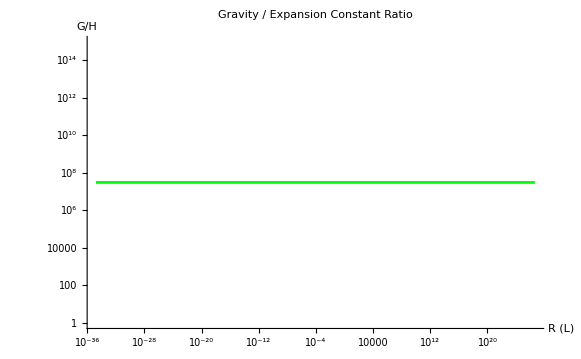

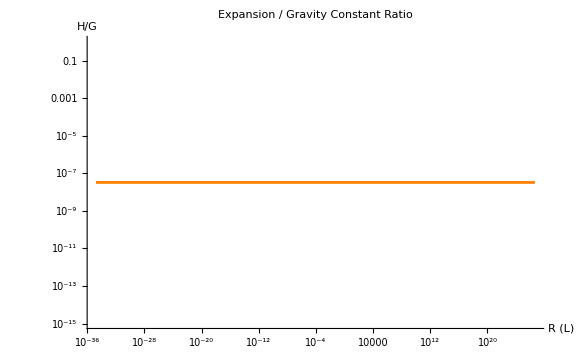

```mathematica
(*Wave Theory Acceleration Ratios*)
Fge[r_]:= (c^2/(Pi*r) / (Pi*c/r) );
Feg[r_]:=(Pi*c/r) / (c^2/(Pi*r));

Show[
LogLogPlot[Fge[r],{r,Lplanck,R},AxesLabel->{"R (L)","G/H"},PlotLabel->"Gravity / Expansion Constant Ratio",PlotStyle->Green]
]

Show[
LogLogPlot[Feg[r],{r,Lplanck,R},AxesLabel->{"R (L)","H/G"},PlotLabel->"Expansion / Gravity Constant Ratio",PlotStyle->Orange]
]
```

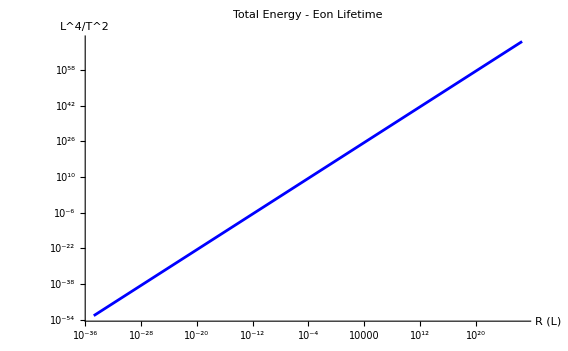

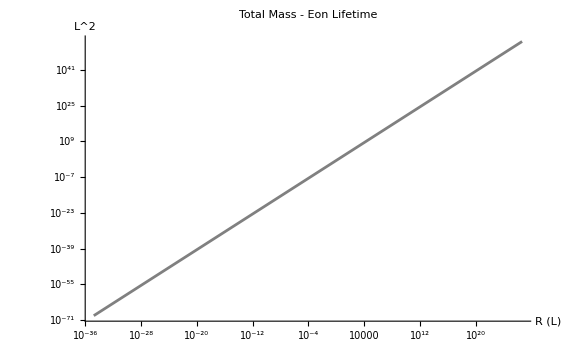

```mathematica
(*Wave Theory Total Energy*)
Fte[r_]:=(Pi*c^2*r^2);
Ftm[r_]:=(Pi*r^2);

Show[
LogLogPlot[Fte[r],{r,Lplanck, R},AxesLabel->{"R (L)","L^4/T^2"},PlotLabel->"Total Energy - Eon Lifetime",PlotStyle->Blue]
]

Show[
LogLogPlot[Ftm[r],{r,Lplanck, R},AxesLabel->{"R (L)","L^2"},PlotLabel->"Total Mass - Eon Lifetime",PlotStyle->Gray]
]
```

```mathematica
(*Wave Theory Energy Density*)
Fwted[r_]:=(Pi*c^2/r);

Show[
LogLinearPlot[
Fwted[r],
{r,Lplanck, 3*10^8},
AxesLabel->{"R (L)","L/T^2"},
PlotLabel->"Energy Density - first second",
PlotStyle->Red]
]

Show[
LogLinearPlot[
Fwted[r],
{r,Lplanck, R},
AxesLabel->{"R (L)","L/T^2"},
PlotLabel->"Energy Density - Eon Lifetime",
PlotStyle->Blue]
]
```

-Graphics-

-Graphics-

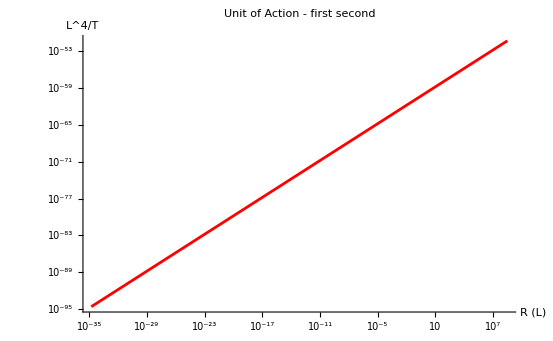

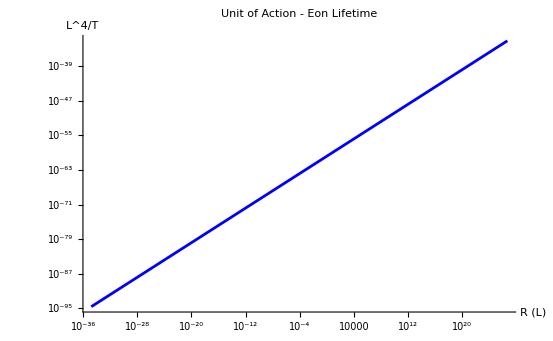

```mathematica
(*Wave Theory Unit of Action*)
Fwtuofa[r_]:=(2*Pi^2*Lplanck^3*r/Tplanck);

Show[
LogLogPlot[Fwtuofa[r],{r,Lplanck, 3*10^8},AxesLabel->{"R (L)","L^4/T"},PlotLabel->"Unit of Action - first second",PlotStyle->Red]
]

Show[
LogLogPlot[Fwtuofa[r],{r,Lplanck, R},AxesLabel->{"R (L)","L^4/T"},PlotLabel->"Unit of Action - Eon Lifetime",PlotStyle->Blue]
]
```

```mathematica
(*Wave Theory Eon Infation Period*)

Fwted[r_]:=(Pi*c^2)/r; (*Wave Theory Energy Density*)
Fwtea[r_]:=(Pi*c)/r;  (*Wave Theory Expansion Acceleration*)
Fwtga[r_]:=c^2/(Pi*r); (*Wave Theory Gravitational Acceleration*)

LogLinearPlot[
{Fwted[r],Fwtea[r],Fwtga[r]},
{r,Lplanck,1},
PlotStyle->{Red,Blue,Green},PlotLegends->{
"WT Energy Density",
"WT Expansion Acceleration",
"WT Gravitational Acceleration"},
AxesLabel->{"R (L)","Value"},
PlotLabel->Style["Wave Theory Eon Infation Period\nL < 1 m\nT < 3.33×10^−9 sec",Bold,14],
ImageSize->Large]
```

-Graphics-

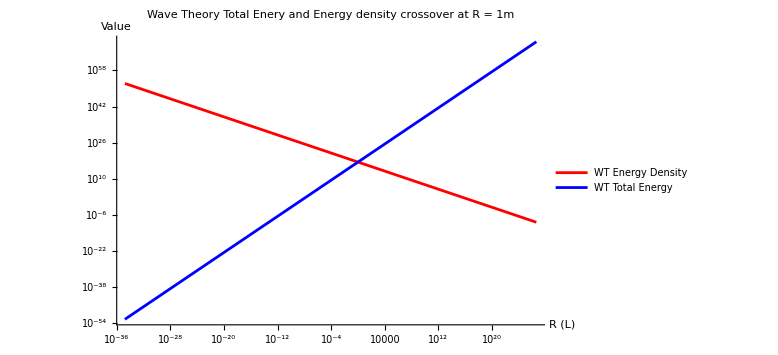

```mathematica
(*Wave Theory Total Enery with Energy density scaling*)

Fwted[r_]:=(Pi*c^2)/r; (*Wave Theory Energy Density*)
Fte[r_]:=(Pi*c^2*r^2); (*Wave Theory Total Energy*)

LogLogPlot[
{Fwted[r],Fte[r]},
{r,Lplanck,R},
PlotStyle->{Red,Blue},PlotLegends->{
"WT Energy Density",
"WT Total Energy"},
AxesLabel->{"R (L)","Value"},
PlotLabel->Style["Wave Theory Total Enery and Energy density crossover at R = 1m",Bold,14],
ImageSize->Large]
```

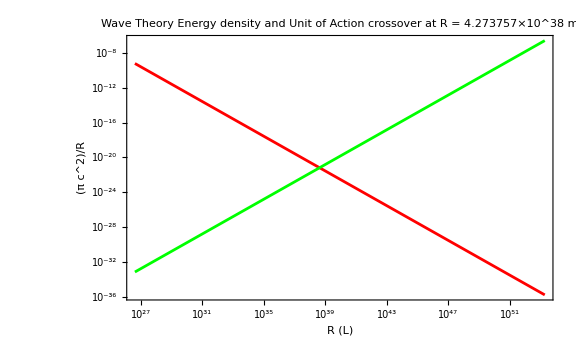

```mathematica
(*Wave Theory Energy density and Unit of Action crossover - Eon Reset*)

Fwted[r_]:=(Pi*c^2)/r; (*Wave Theory Energy Density*)
Fwtuofa[r_]:=(2*Pi^2*Lplanck^3*r/Tplanck); (*Wave Theory Unit of Action*)

Show[
LogLogPlot[
Fwted[r],
{r,R,R^2},
PlotStyle->Red,
Frame->True,
FrameLabel->{{"\!\(\*FractionBox[\(π c\^2\), \(R\)]\)","\!\(\*FractionBox[\(2 π\^2 Lp\^3 R\), \(Tp\)]\)"},{"R (L)",None}},FrameTicks->{Automatic,(*bottom*)Automatic,(*left*)None,(*top*)Automatic (*right,added below*)},
FrameStyle->{{Red,Green},{None,None}},
PlotRange->All,Axes->False],

LogLogPlot[
Fwtuofa[r],
{r,R,R^2},
PlotStyle->Green,
Frame->True,
FrameLabel->{{None,"\!\(\*FractionBox[\(2 π\^2 Lp\^3 R\), \(Tp\)]\)"},{None,None}},FrameTicks->{None,(*bottom*)None,(*left*)None,(*top*)Automatic (*right*)},
FrameStyle->{{Red, Green},{None,None}},
PlotRange->All,Axes->False],

PlotLabel->Style["Wave Theory Energy density and Unit of Action crossover at R = 4.273757×10^38 m",Bold,14],
ImageSize->Large,
PlotLegends->Placed[LineLegend[{Red,Green},{"WT Energy Density","WT Unit of Action"}],Below]]
```

```mathematica
(*Wave Theory Eon Reset Radius and Universe age*)

c=2.99792*10^8;  (*Speed of light in meters per second*)
Lplanck=1.616255*10^-35; (*Planck length in meters*)
Tplanck = 5.391247*10^-44; (*Planck time in seconds*)

(*Define the Radius of the Eon reset event*)
REonResetR = N[Sqrt[c/(2*Pi*Lplanck^2)],15];

(*Define age of Eon for the Eon reset event*)
REonResetAge = N[REonResetR / c,15];
REonResetAgeTTY = N[REonResetAge / (3600*24*365.25) /  10^9/ 10^12, 15];

(*Calculate the Vacuum Energy Density*)
energyDensity=N[Pi*c^2/REonResetR,15];

(*Compute Planck Constant - WT Unit of Action*)
unitAction = N[(2*Pi^2*REonResetR*Lplanck^3)/Tplanck, 15];

(*Display Results*)
Dataset[<|
"R of Eon reset (m) (L)"->NumberForm[REonResetR,{50,15}],
"Age of Eon when reset (s) (T)"->NumberForm[REonResetAge,{50,15}],
"Age of Eon when reset billion*trillion years"->NumberForm[REonResetAgeTTY,{50,15}],
"Vacuum Energy Density (J/m.b3) (L/T^2)"->NumberForm[energyDensity,{50,15}],
"Unit of Action (Js) (L^4/T)"->NumberForm[unitAction,{50,15}]|>]
```